## Error Analysis

Prepared with the help of chatgpt: 
See https://chatgpt.com/share/66fe55e3-ecd0-8007-9d39-ae15c09faa08 
for the chat

```mathematica
(*Set Directoy to the one notebook is running*)
SetDirectory[NotebookDirectory[]]
```

/Users/sbilmis/Desktop

-Graphics-

-Graphics-

```mathematica
f[M_,m_]= g (M-m)/(M+m)
```

(g (M-m))/(m+M)

```mathematica
AroundReplace[f[M,m],{
m->Around[50,1],
M->Around[100,1],
g->9.80
} ]//ScientificForm
```

3.270.10

```mathematica
AroundReplace[GAMMA[gAA, mTT,mAA,mPP],{
mTT->2.74,
mAA->2.4221,
mPP->0.13957,
gAA->Around[-4.31 ,0.20]
} ]//ScientificForm
```

```mathematica
m=Around[50,1]
M=Around[100,1]
g=9.80
f[M,m]
```

50.01.0

100.01.0

9.8

3.270.10

```mathematica
(*Define the function f with Around for uncertainties*)f[M_,m_]:=g (M-m)/(M+m)

(*Use Around to include uncertainties in M and m*)
f[Around[100,1],Around[50,1]]
```

3.270.10

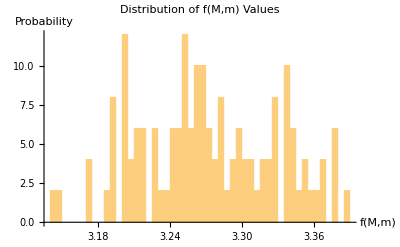

{3.27197,0.0571474,-Graphics-}

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Calculate the mean and standard deviation of the results*)
meanValue=Mean[results];
stdDev=StandardDeviation[results];

(*Plot the histogram of the results*)histogram=Histogram[results,50,"PDF",PlotLabel->"Distribution of f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}]

(*Display the mean,standard deviation,and the histogram*)
{meanValue,stdDev,histogram}
```

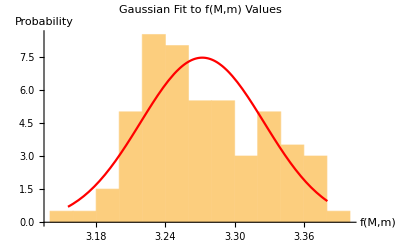
{{μ→3.27198,σ→0.0535263},-Graphics-}

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay*)
histogram=Show[Histogram[results,10,"PDF",PlotLabel->"Gaussian Fit to f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->Red]];

(*Display the fitted parameters and the histogram*)
{fit,histogram}
```

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)
histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to f(M,m) Values",Bold,16],AxesLabel->{Style["f(M,m)",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];

{fit,histogram}

(*Export the plot to a PDF file*)
Export["GaussianFit_Histogram.pdf",histogramPlot,"PDF"]
```

{{μ→3.26238,σ→0.055061},-Graphics-}

GaussianFit_Histogram.pdf

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_List,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{randomParams,results,fit,histogramPlot},(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,params}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with uncertainties as {value,uncertainty}*)
params={{100,1},{50,1}}; (*M=100±1,m=50±1*)

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

## Generic Function

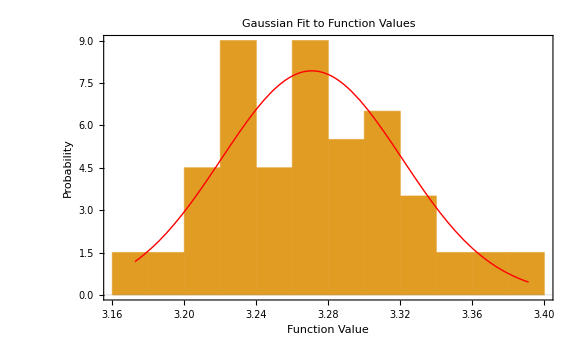
{{μ→3.27085,σ→0.050314},-Graphics-}

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

```mathematica
?Histogram
```

THIS IS FINAL FORM: USE THIS ONE:

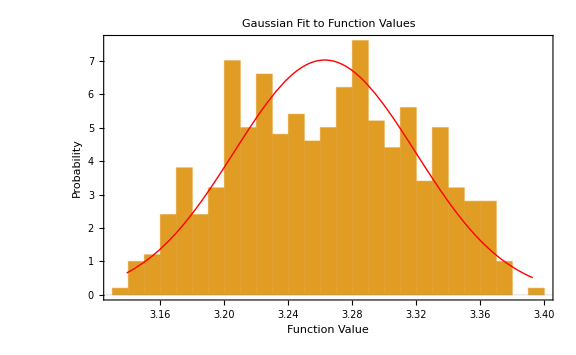
{{μ→3.26276,σ→0.0568428},-Graphics-}

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

```mathematica
ResourceSearch["monte carlo"]
```

```mathematica
$Path
```

{/Users/sbilmis/Library/Mathematica/DocumentationIndices,/Users/sbilmis/heptools/analysis/hep/FEYNARTS/FeynArts,/Users/sbilmis/heptools/analysis/hep/FEYNARTS/FormCalc,/Users/sbilmis/heptools/analysis/hep/FEYNARTS/LoopTools,/Users/sbilmis/analysis/hep/FEYNARTS/FeynArts,/Users/sbilmis/analysis/hep/FEYNARTS/LoopTools,/Users/sbilmis/analysis/hep/qcd_sum,/Applications/Mathematica.app/Contents/SystemFiles/Links,/Users/sbilmis/Library/Mathematica/Kernel,/Users/sbilmis/Library/Mathematica/Autoload,/Users/sbilmis/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/sbilmis,/Applications/Mathematica.app/Contents/AddOns/Packages,/Applications/Mathematica.app/Contents/SystemFiles/Autoload,/Applications/Mathematica.app/Contents/AddOns/Autoload,/Applications/Mathematica.app/Contents/AddOns/Applications,/Applications/Mathematica.app/Contents/AddOns/ExtraPackages,/Applications/Mathematica.app/Contents/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Contents/Documentation/English/System,/Applications/Mathematica.app/Contents/SystemFiles/Data/ICC,/Applications/Mathematica.app/Contents/Documentation/ChineseSimplified/System/}

```mathematica
SystemOpen[$UserBaseDirectory<>"/Kernel/init.m"]
```